```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\PVP10_EG_Ag\isotac-para\111Ag\12_pmf\equilibrate\2_NPT_GenIC

```mathematica
log=OpenRead["thermo.lammps"]
```

InputStream[thermo.lammps,66]

```mathematica
Find[log,"Step PotEng"]
```

# Step PotEng KinEng TotEng Temp Volume Press Lx Lz Pxx Pyy Pzz

```mathematica
thermo=ReadList[log,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}]
```

{{5828001,-13871.8,1325.9,-12545.9,300.863,342074.,-291.63,46.36,147.025,-425.895,-438.896,-10.0994},{«1»},«997»,{5829000,-13873.5,1318.22,-12555.3,«4»,146.903,-147.744,-500.349,-1018.28}}

```mathematica
Close[log];
```

```mathematica
log=OpenRead["thermo_long.lammps"];
Find[log,"Step PotEng"];
thermolong=ReadList[log,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
Close[log];
```

```mathematica
CreateDirectory["graph"];
```

```mathematica
Vavg=Mean[thermolong[[All,6]]]
```

341772.

```mathematica
Nearest[thermo[[All,6]],Vavg]
```

{341772.}

```mathematica
Position[thermo[[All,6]],Nearest[thermo[[All,6]],Vavg][[1]]]
```

{{956}}

```mathematica
chosentimestep=thermo[[Flatten[Position[thermo[[All,6]],Nearest[thermo[[All,6]],Vavg][[1]]]]]]
```

{{5828956,-13879.,1323.9,-12555.1,300.408,341772.,18.0339,46.3652,146.863,-231.189,-93.9914,379.282}}

```mathematica
Export["report.txt",{"Chosen timestep:",chosentimestep[[1,1]]," ","Volume:",chosentimestep[[1,6]]," ","Pressure:",chosentimestep[[1,7]]}]
```

report.txt

```mathematica
timeprod=1;
thermotimestep=1;
timestepps=0.001;
```

```mathematica
Tavg=Mean[thermo[[All,5]]]
```

300.209

```mathematica
Tstd=StandardDeviation[thermo[[All,5]]]
```

1.24735

```mathematica
TStdErr=Tstd/(Length[thermo])^0.5
```

0.0394446

```mathematica
Tavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],5]]]
```

300.209

```mathematica
Tstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],5]]]
```

1.24735

```mathematica
TStdErr2=Tstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

0.0394446

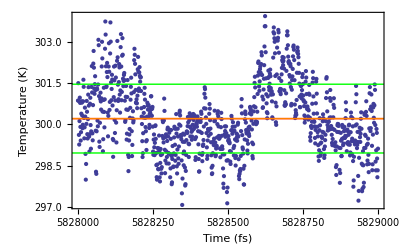

```mathematica
Tprofile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,5]]],2],1;;-1]],Plot[{Tavg,Tavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Tavg2+Tstd2,Tavg2-Tstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Temperature (K)"}]
```

```mathematica
Export["graph/Temp_profile.png",Tprofile,ImageResolution->100]
```

graph/Temp_profile.png

```mathematica
Pavg=Mean[thermo[[All,7]]]
```

5.07818

```mathematica
Pstd=StandardDeviation[thermo[[All,7]]]
```

407.101

```mathematica
PStdErr=Pstd/(Length[thermo])^0.5
```

12.8737

```mathematica
Pavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],7]]]
```

5.07818

```mathematica
Pstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],7]]]
```

407.101

```mathematica
PStdErr2=Pstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

12.8737

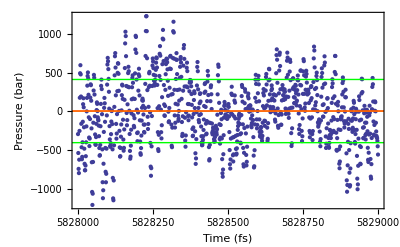

```mathematica
PProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,7]]],2],1;;-1]],Plot[{Pavg,Pavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Pavg2+Pstd2,Pavg2-Pstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Pressure (bar)"}]
```

```mathematica
Export["graph/Pressure_profile.png",PProfile,ImageResolution->100]
```

graph/Pressure_profile.png

```mathematica
Volavg=Mean[thermo[[All,6]]]
```

341103.

```mathematica
Volstd=StandardDeviation[thermo[[All,6]]]
```

455.731

```mathematica
VolStdErr=Volstd/(Length[thermo])^0.5
```

14.4115

```mathematica
Volavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],6]]]
```

341103.

```mathematica
Volstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],6]]]
```

455.731

```mathematica
VolStdErr2=Volstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

14.4115

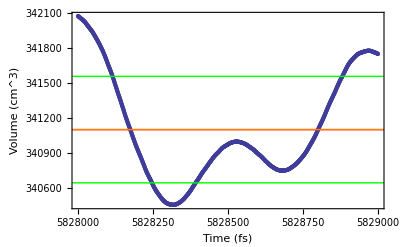

```mathematica
VProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,6]]],2],1;;-1]],Plot[{Volavg,Volavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Volavg2+Volstd2,Volavg2-Volstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Volume (cm^3)"}]
```

```mathematica
Export["graph/Volume_profile.png",VProfile,ImageResolution->100]
```

graph/Volume_profile.png

```mathematica
Engavg=Mean[thermo[[All,2]]]
```

-13871.1

```mathematica
Engstd=StandardDeviation[thermo[[All,2]]]
```

5.97781

```mathematica
EngStdErr=Engstd/(Length[thermo])^0.5
```

0.189035

```mathematica
Engavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],2]]]
```

-13871.1

```mathematica
Engstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],2]]]
```

5.97781

```mathematica
EngStdErr2=Engstd2/(Length[thermo[[timeprod/thermotimestep;;Length[thermo],5]]])^0.5
```

0.189035

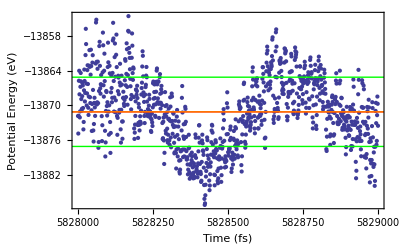

```mathematica
EProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,2]]],2],1;;-1]],Plot[{Engavg,Engavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Engavg2+Engstd2,Engavg2-Engstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Potential Energy (eV)"}]
```

```mathematica
Export["graph/Energy_profile.png",EProfile,ImageResolution->100]
```

graph/Energy_profile.png

```mathematica
Lzavg=Mean[thermo[[All,9]]]
```

146.743

```mathematica
Lzstd=StandardDeviation[thermo[[All,9]]]
```

0.129116

```mathematica
Lzavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],9]]]
```

146.743

```mathematica
Lzstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],9]]]
```

0.129116

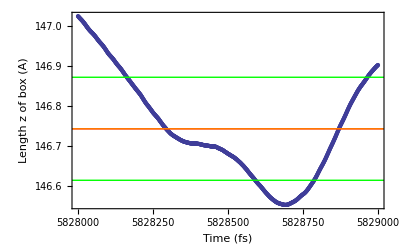

```mathematica
LzProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,9]]],2],1;;-1]],Plot[{Lzavg,Lzavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Lzavg2+Lzstd2,Lzavg2-Lzstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Length z of box (A)"}]
```

```mathematica
Export["graph/Lz_profile.png",LzProfile,ImageResolution->100]
```

graph/Lz_profile.png

```mathematica
Lxavg=Mean[thermo[[All,8]]]
```

46.3387

```mathematica
Lxstd=StandardDeviation[thermo[[All,8]]]
```

0.0220398

```mathematica
Lxavg2=Mean[thermo[[timeprod/thermotimestep;;Length[thermo],8]]]
```

46.3387

```mathematica
Lxstd2=StandardDeviation[thermo[[timeprod/thermotimestep;;Length[thermo],8]]]
```

0.0220398

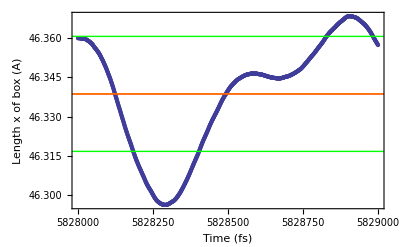

```mathematica
LxProfile=Show[ListPlot[Part[Partition[Riffle[thermo[[All,1]],thermo[[All,8]]],2],1;;-1]],Plot[{Lxavg,Lxavg2},{x,0,100000000},PlotStyle->{{Red,Thick},{Orange,Thick}}],Plot[{Lxavg2+Lxstd2,Lxavg2-Lxstd2},{x,0,100000000},PlotStyle->{{Green,Thick},{Green,Thick}}],Frame->True,FrameLabel->{"Time (fs)","Length x of box (A)"}]
```

```mathematica
Export["graph/Lx_profile.png",LxProfile,ImageResolution->100]
```

graph/Lx_profile.png